# 0) Preliminaries

```mathematica
plotFun[fun_,lims_,epilog_,label_,legs_:None]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{Full,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLegends->legs,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]
```

```mathematica
discPlotFun[fun_,range_,lims_,epilog_,label_]:=Framed@DiscretePlot[fun,{n,range[[1]],range[[2]]},PlotRange->lims,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}]
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,maxran_,limit_,label_,epilog_:{}]:=Module[{funplot,epsplot},
funplot=DiscretePlot[fun[n],{n,0,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{{Line[{{0,limit},{maxran,limit}}],Arrow[{{(*maxran-20*)20,limit+.05},{(*maxran-25*)15,limit}}],Text["lim_(n → ∞) a_n="<>ToString[limit],{(*maxran-20*)22,limit+.05},Left]},{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]},Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,.2},0.0001,.2,Appearance->"Open" }
]
]*)
```

# 1) Schwerpunkt

v_1,v_2,v_3∈ℝ^2

w_1=1/2(v_2+v_3), w_2=1/2(v_1+v_3), w_3=1/2(v_1+v_2)

G_(v_i,w_i-v_i)={v_i+λ·(w_i-v_i), λ∈ℝ}, i=1,2,3

Intersection point?

## Graphically

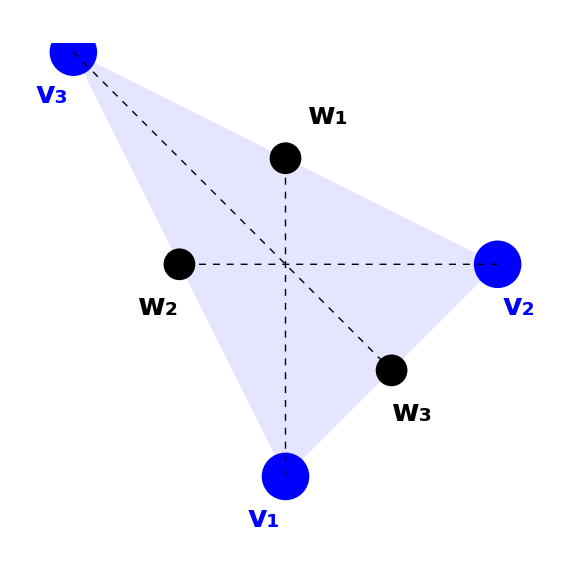

```mathematica
v1={0,0};
v2={1,1};
v3={-1,2};
w1=(v2+v3)/2;
w2=(v1+v3)/2;
w3=(v2+v1)/2;
Graphics[{{Opacity[.1],Blue,Triangle[{v1,v2,v3}]},{Text[Style["v_1",30,Blue,Bold],{-.1,-.2}],Text[Style["v_2",30,Blue,Bold],{1+.1,1-.2}],Text[Style["v_3",30,Blue,Bold],{-1-.1,2-.2}],
Blue,PointSize[.06],Point[{v1,v2,v3}]},{Text[Style["w_2",30,Black,Bold],{-.5-.1,1-.2}],Text[Style["w_3",30,Black,Bold],{.5+.1,.3}],Text[Style["w_1",30,Black,Bold],{.2,1.7}],Black,PointSize[.04],Point[{w1,w2,w3}]},{Dashed,Line[{{v1,w1},{v2,w2},{v3,w3}}]}},Axes->False]
```

## Solution

The intersection point p lies in all G_(v_1,w_1-v_1), G_(v_2,w_2-v_2) and G_(v_3,w_3-v_3) and so:

p=v_1+λ_1(w_1-v_1) ∧ p=v_2+λ_2(w_2-v_2) ∧ p=v_3+λ_3(w_3-v_3)

Then v_1+λ_1(w_1-v_1)=v_2+λ_2(w_2-v_2) and so:

v_1+λ_1(1/2(v_2+v_3)-v_1)=v_2+λ_2(1/2(v_1+v_3)-v_2)

By rearranging the terms in the equation above we get:

(1-λ_1-λ_2/2)v_1+(λ_1/2-1+λ_2)v_2+(λ_1/2-λ_2/2)v_3=0

As vertices v_1,v_2,v_3 represent a non-degenerate triangle, they correspond to linearly independent vectors and therefore:

1-λ_1-λ_2/2=0 ∧λ_1/2-1+λ_2=0 ∧ λ_1/2-λ_2/2=0

Solving this system of equations yields λ_1=λ_2=2/3. Analogously we can proceed to find the value of λ_3=2/3. The intersection point is thus p=v_1+λ_1(w_1-v_1)=v_1+2/3(1/2(v_2+v_3)-v_1)=(v_1+v_2+v_3)/3 and so:

p=(v_1+v_2+v_3)/3

Point p is called an orthocenter of the triangle given by vertices v_1,v_2,v_3.

# 2) Normalenvektor

G_(v,t)={v+λ·t, λ∈ℝ};   v,t∈ℝ^n, t≠0

w∈G_(v,t)
⟨w,t⟩=0

w=? 
||w'||≥||w|| ?

## Graphically

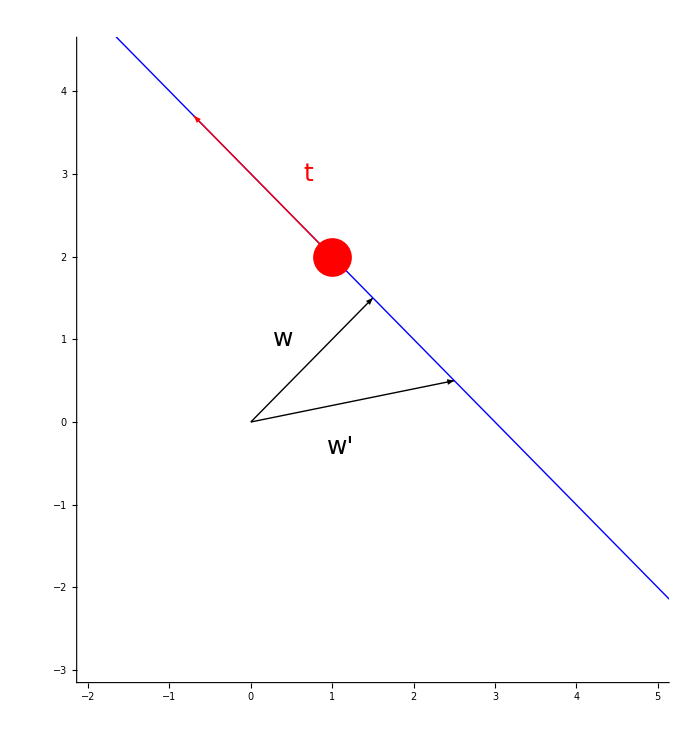

```mathematica
Framed@Graphics[{{Thick,Blue,InfiniteLine[{1,2},{1,-1}]},{Red,PointSize[.04],Point[{1,2}]},{Red,Thick,Arrowheads[.07],Arrow[{{1,2},{1,2}-1.7{1,-1}}],Text[Style["t",25,Red],{.7,3}]},{Arrow[{{0,0},1.5{1,1}}],Text[Style["w",25],{.4,1}]},
{Arrow[{{0,0},{1,2}+1.5{1,-1}}],Text[Style["w'",25],{1.1,-.3}]}
},Axes->True,PlotRange->{{-2,5},{-3,4.5}}]
```

## Solution

## a)

We have 0=⟨w,t⟩=⟨v+λ_0 t,t⟩=⟨v,t⟩+λ_0⟨t,t⟩ and thus λ_0=-⟨w,t⟩/⟨t,t⟩. Therefore:

w=v+(-⟨w,t⟩/⟨t,t⟩)t

## b)

For any w' we can write w'=v+λ t=(v+λ_0 t)+(λ-λ_0)t=w+μ t for some μ∈ℝ. Then

Possibility 1

||w'(||)^2=||w+μ t(||)^2=⟨w+μ t,w+μ t⟩=
⟨w,w⟩+2μ ⟨w,t⟩+μ^2⟨t,t⟩=||w(||)^2+μ^2||t(||)^2   since   ⟨w,t⟩=0

As μ^2||t||≥0 we get ||w'(||)^2≥||w(||)^2 and thus ||w'||≥||w||.

Possibility 2

⟨w,w'⟩=⟨w,w+μ t⟩=⟨w,w⟩+μ ⟨w,t⟩=||w(||)^2 ... (1)    since   ⟨w,t⟩=0

Cauchy–Schwarz inequality: ⟨w,w'⟩≤ ||w||·||w'|| ... (2)

Together (1) and (2): ||w(||)^2≤ ||w||·||w'||, from where ||w||≤||w'||.

The final inequality basically means that there is no other point on the line G_(v,t) that is closer to the origin than w.

# 3) Lineare (Un)abhängigkeit

v_1=1/(√3)(1
1
1), v_2=(0
1
0), v_3=1/(√2)(1
0
1)

(v_1, v_2,v_3) is linearly independent?

v_4=?,  ||v_4||=1, ⟨v_4,v_1⟩=0 ∧ ⟨v_4,v_2⟩=0

Angle between v_4 and v_3?

## Graphically

```mathematica
Framed@Graphics3D[{{Arrow[{{{0,0,0},1/(√3){1,1,1}},{{0,0,0},{0,1,0}},{{0,0,0},1/(√2){1,0,1}}}],
Text[Style["v_1",25,Bold],1/(√3){1,1,1},{-2,-1}],Text[Style["v_2",25,Bold],{0,1,0},{-1,-1}],Text[Style["v_3",25,Bold],1/(√2){1,0,1},{-1,-1}]},{Blue,Arrow[{{0,0,0},1/(√2){1,0,-1}}]},Text[Style["v_4",25,Bold,Blue],1/(√2){1,0,-1},{-1,-1}]},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

## Solution

## a) Linear independence

Consider the following linear combination:

α_1 v_1+α_2 v_2+α_3 v_3=α_1 1/(√3)(1
1
1)+α_2(0
1
0)+α_3 1/(√2)(1
0
1)=(α_1/(√3)+α_3/(√2)
α_1/(√3)+α_2
α_1/(√3)+α_3/(√2))

For which α_i is this expression equal to the zero vector?

α_1 v_1+α_2 v_2+α_3 v_3=0?

The following conditions have to be satisfied:

α_1/(√3)+α_3/(√2)=0 ∧ α_1/(√3)+α_2=0

For which we get solution: α_2=-1/(√3)α_1, α_3=-(√2)/(√3)α_1, α_1∈ℝ.

The vectors are therefore linearly DEPENDENT.

## b) v_4

Let us have a vector of a form v_4=(a
b
c).

This vector has to satisfy ⟨v_4,v_1⟩=1/(√3)(a+b+c)=0 and ⟨v_4,v_2⟩=b=0. It is satisfied for b=0 and c=-a.

Also ||v_4||=a^2+b^2+c^2=2 a^2=1 and thus a=1/(√2).

We can conclude v_4=1/(√2)(1
0
-1).

## c) Angle

v_4=1/(√2)(1
0
-1).

As ⟨v_4,v_3⟩=0 we have cos(θ)=⟨v_4,v_3⟩/(||v_4||·||v_3||)=0 and thus θ=π/2. Vectors v_3 and v_4 are orthogonal to each other.